```mathematica
ElastoPlastic[epsp_,EP_,ETotal_]:=Block[{epspnext,θnext,EPnext,valf2,SigI1xJ2,EElast,delepsp,I1next,J2next,lval,diffsig,sigresult,pr},
pr=True;
epspnext=epsp;
EElast=ETotal-EP;
SigI1xJ2={K EElast[[1]],2G EElast[[2]]}/.exemple;
valf2=Function2[SigI1xJ2[[1]],SigI1xJ2[[2]],epsp]//Chop;
If[pr,
Print["ETotal = ",ETotal];
Print["SigI1xJ2 = ",SigI1xJ2];
Print["valf2 = ",valf2]
];
If[valf2<= 0,
epspnext = epsp;
sigresult=SigI1xJ2;
EPnext=EP
,
{θnext,delepsp}=NewtonFunc2[epsp,SigI1xJ2];
epspnext=epsp+delepsp;
lval=LFunction[epspnext];
I1next=lval+F[lval]R Cos[θnext]/.exemple;
J2next=F[lval]Sin[θnext]/.exemple;
Print["Function2 = ",Function2[I1next,J2next,epspnext]];
sigresult={I1next,J2next};
diffsig=SigI1xJ2-{I1next,J2next};
EPnext=EP+{diffsig[[1]]/K,diffsig[[2]]/(2G)}/.exemple;
];
{epspnext,EPnext,sigresult}
]
locepsp=0;
EP={0,0};
ETotal={-0.0,0.0};
ElastoPlastic[locepsp,EP,ETotal]
```

ETotal = {0.,0.}

SigI1xJ2 = {0.,0.}

valf2 = 0

{0,{0,0},{0.,0.}}

```mathematica
ListETotal=Table[{epsa,-epsa/Sqrt[3]},{epsa,0,-0.065,-0.065/20}]
(*ListETotal=Join[ListETotal,Reverse[ListETotal]]*)
Result={{0,{0,0},{0,0}}};
Result[[-1,1]]
Result[[-1,2]]
ElastoPlastic[Result[[-1,1]],Result[[-1,2]],ListETotal[[1]]]

For[i=2,i<=Length[ListETotal],i++,
AppendTo[Result,ElastoPlastic[Result[[-1,1]],Result[[-1,2]],ListETotal[[i]]]]
]
```

{{0.,0.},{-0.00325,0.00187639},{-0.0065,0.00375278},{-0.00975,0.00562917},{-0.013,0.00750555},{-0.01625,0.00938194},{-0.0195,0.0112583},{-0.02275,0.0131347},{-0.026,0.0150111},{-0.02925,0.0168875},{-0.0325,0.0187639},{-0.03575,0.0206403},{-0.039,0.0225167},{-0.04225,0.024393},{-0.0455,0.0262694},{-0.04875,0.0281458},{-0.052,0.0300222},{-0.05525,0.0318986},{-0.0585,0.033775},{-0.06175,0.0356514},{-0.065,0.0375278}}

0

{0,0}

ETotal = {0.,0.}

SigI1xJ2 = {0.,0.}

valf2 = 0

{0,{0,0},{0.,0.}}

ETotal = {-0.00325,0.00187639}

SigI1xJ2 = {-0.216667,0.150111}

valf2 = 13.8654

residue = {0.0276382,0.00346752}

residue = {0.0146829,1.05203×10^-6}

residue = {-9.25785×10^-6,1.15613×10^-7}

residue = {5.4468×10^-11,-2.14035×10^-14}

residue = {0.,1.73472×10^-18}

residue = {0.,4.33681×10^-19}

residue = {0.,0.}

residue = {0.,0.}

Function2 = 2.22045×10^-16

ETotal = {-0.0065,0.00375278}

SigI1xJ2 = {-0.254327,0.18266}

valf2 = 13.7689

residue = {-0.038087,0.00330968}

residue = {0.0198114,-8.47344×10^-6}

residue = {-0.0000109871,1.87415×10^-7}

residue = {1.26571×10^-10,-6.57278×10^-14}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 3.33067×10^-16

ETotal = {-0.00975,0.00562917}

SigI1xJ2 = {-0.301914,0.191817}

valf2 = 12.0778

residue = {0.00297442,0.00315006}

residue = {0.0157106,1.22835×10^-6}

residue = {-0.0000112272,1.26491×10^-7}

residue = {7.6279×10^-11,-3.14852×10^-14}

residue = {-4.44089×10^-16,2.1684×10^-18}

residue = {8.88178×10^-16,-3.03577×10^-18}

residue = {-4.44089×10^-16,2.60209×10^-18}

residue = {0.,-2.1684×10^-18}

Function2 = 1.11022×10^-16

ETotal = {-0.013,0.00750555}

SigI1xJ2 = {-0.355988,0.197212}

valf2 = 10.6312

residue = {0.0192513,0.00308518}

residue = {0.014327,5.74698×10^-6}

residue = {-0.0000118631,1.11803×10^-7}

residue = {7.00928×10^-11,-2.14685×10^-14}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

«1 more identical outputs»

Function2 = 1.11022×10^-16

ETotal = {-0.01625,0.00938194}

SigI1xJ2 = {-0.41322,0.201726}

valf2 = 9.44542

residue = {0.0287989,0.00304737}

residue = {0.0137375,8.69705×10^-6}

residue = {-0.0000127609,1.07998×10^-7}

residue = {7.39666×10^-11,-1.66377×10^-14}

residue = {0.,1.30104×10^-18}

residue = {0.,4.33681×10^-19}

residue = {0.,0.}

residue = {0.,0.}

Function2 = 0.

ETotal = {-0.0195,0.0112583}

SigI1xJ2 = {-0.472683,0.206044}

valf2 = 8.4676

residue = {0.0367432,0.00301619}

residue = {0.0133292,0.0000113819}

residue = {-0.0000138198,1.06461×10^-7}

residue = {8.07248×10^-11,-1.18347×10^-14}

residue = {4.44089×10^-16,-1.30104×10^-18}

residue = {-4.44089×10^-16,4.33681×10^-19}

residue = {4.44089×10^-16,-8.67362×10^-19}

residue = {-4.44089×10^-16,4.33681×10^-19}

Function2 = 0.

ETotal = {-0.02275,0.0131347}

SigI1xJ2 = {-0.534167,0.210361}

valf2 = 7.65232

residue = {0.0446501,0.00298534}

residue = {0.0128926,0.0000142677}

residue = {-0.0000149649,1.04516×10^-7}

residue = {8.76845×10^-11,-5.04327×10^-15}

residue = {-4.44089×10^-16,1.30104×10^-18}

residue = {4.44089×10^-16,-8.67362×10^-19}

residue = {-4.44089×10^-16,8.67362×10^-19}

residue = {4.44089×10^-16,-8.67362×10^-19}

Function2 = 2.22045×10^-16

ETotal = {-0.026,0.0150111}

SigI1xJ2 = {-0.597675,0.214737}

valf2 = 6.96509

residue = {0.0530615,0.00295268}

residue = {0.0123396,0.0000175604}

residue = {-0.0000161068,1.0114×10^-7}

residue = {9.31046×10^-11,4.6226×10^-15}

residue = {0.,8.67362×10^-19}

residue = {4.44089×10^-16,-3.46945×10^-18}

residue = {0.,2.1684×10^-18}

residue = {4.44089×10^-16,-3.03577×10^-18}

Function2 = -1.11022×10^-16

ETotal = {-0.02925,0.0168875}

SigI1xJ2 = {-0.663277,0.219196}

valf2 = 6.37998

residue = {0.0622142,0.00291732}

residue = {0.0116178,0.0000213905}

residue = {-0.0000170977,9.58334×10^-8}

residue = {9.52829×10^-11,1.68953×10^-14}

residue = {0.,3.03577×10^-18}

residue = {8.88178×10^-16,-4.33681×10^-18}

residue = {-8.88178×10^-16,3.03577×10^-18}

residue = {0.,1.73472×10^-18}

Function2 = -3.33067×10^-16

ETotal = {-0.0325,0.0187639}

SigI1xJ2 = {-0.73107,0.223748}

valf2 = 5.87739

residue = {0.072256,0.00287872}

residue = {0.0106818,0.0000258748}

residue = {-0.0000176835,8.82823×10^-8}

residue = {9.23173×10^-11,2.96629×10^-14}

residue = {0.,2.60209×10^-18}

residue = {0.,8.67362×10^-19}

residue = {0.,4.33681×10^-19}

residue = {0.,0.}

Function2 = 1.11022×10^-16

ETotal = {-0.03575,0.0206403}

SigI1xJ2 = {-0.801164,0.228398}

valf2 = 5.44225

residue = {0.0833134,0.00283647}

residue = {0.00948312,0.0000311376}

residue = {-0.0000174378,7.8259×10^-8}

residue = {8.23128×10^-11,3.79067×10^-14}

residue = {4.44089×10^-16,-1.73472×10^-18}

residue = {4.44089×10^-16,-8.67362×10^-19}

residue = {4.44089×10^-16,-8.67362×10^-19}

residue = {4.44089×10^-16,-8.67362×10^-19}

Function2 = 1.66533×10^-16

ETotal = {-0.039,0.0225167}

SigI1xJ2 = {-0.873677,0.233152}

valf2 = 5.06287

residue = {0.0955161,0.00279014}

residue = {0.0079655,0.0000373217}

residue = {-0.0000156649,6.56056×10^-8}

residue = {6.40585×10^-11,3.3831×10^-14}

residue = {-8.88178×10^-16,2.1684×10^-18}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

Function2 = -5.55112×10^-17

ETotal = {-0.04225,0.024393}

SigI1xJ2 = {-0.948733,0.238014}

valf2 = 4.73005

residue = {0.109007,0.00273928}

residue = {0.00606128,0.0000445943}

residue = {-0.0000112547,5.02546×10^-8}

residue = {3.82543×10^-11,1.26184×10^-14}

residue = {-8.88178×10^-16,3.46945×10^-18}

residue = {8.88178×10^-16,-4.77049×10^-18}

residue = {-8.88178×10^-16,4.77049×10^-18}

residue = {8.88178×10^-16,-4.77049×10^-18}

Function2 = 3.33067×10^-16

ETotal = {-0.0455,0.0262694}

SigI1xJ2 = {-1.02646,0.242989}

valf2 = 4.43647

residue = {0.123945,0.00268342}

residue = {0.00368839,0.0000531532}

residue = {-2.46362×10^-6,3.22743×10^-8}

residue = {8.82272×10^-12,-3.52279×10^-15}

residue = {1.33227×10^-15,-5.20417×10^-18}

residue = {0.,4.33681×10^-19}

residue = {0.,0.}

residue = {0.,0.}

Function2 = -5.55112×10^-17

ETotal = {-0.04875,0.0281458}

SigI1xJ2 = {-1.10701,0.248079}

valf2 = 4.17622

residue = {0.140513,0.002622}

residue = {0.000746708,0.0000632329}

residue = {0.0000134135,1.19417×10^-8}

residue = {-1.83698×10^-11,1.10354×10^-13}

residue = {-4.44089×10^-16,4.33681×10^-19}

residue = {-4.44089×10^-16,8.67362×10^-19}

residue = {-4.44089×10^-16,8.67362×10^-19}

residue = {-4.44089×10^-16,8.67362×10^-19}

Function2 = 1.11022×10^-16

ETotal = {-0.052,0.0300222}

SigI1xJ2 = {-1.19052,0.253289}

valf2 = 3.94452

residue = {-0.142815,0.00308996}

residue = {0.06415,-0.0000365899}

residue = {-0.0000860583,1.85783×10^-6}

residue = {2.66669×10^-8,-7.82254×10^-12}

residue = {4.44089×10^-16,-8.67362×10^-19}

residue = {4.44089×10^-16,-8.67362×10^-19}

residue = {4.44089×10^-16,-8.67362×10^-19}

«1 more identical outputs»

Function2 = -3.33067×10^-16

ETotal = {-0.05525,0.0318986}

SigI1xJ2 = {-1.27713,0.258623}

valf2 = 3.73745

residue = {-0.130593,0.0030375}

residue = {0.0651921,-0.0000365386}

residue = {-0.0000982957,1.8862×10^-6}

residue = {3.104×10^-8,-9.60393×10^-12}

residue = {-2.22045×10^-15,6.93889×10^-18}

residue = {2.22045×10^-15,-5.20417×10^-18}

residue = {0.,-4.33681×10^-18}

residue = {-8.88178×10^-16,5.42101×10^-18}

Function2 = 4.44089×10^-16

ETotal = {-0.0585,0.033775}

SigI1xJ2 = {-1.36702,0.264082}

valf2 = 3.55176

residue = {-0.116435,0.00297734}

residue = {0.0657229,-0.0000357379}

residue = {-0.000113724,1.88478×10^-6}

residue = {3.55055×10^-8,-1.16816×10^-11}

residue = {8.88178×10^-16,6.50521×10^-19}

residue = {0.,-8.67362×10^-19}

residue = {0.,-2.1684×10^-19}

residue = {0.,0.}

Function2 = 0.

ETotal = {-0.06175,0.0356514}

SigI1xJ2 = {-1.46033,0.269669}

valf2 = 3.38474

residue = {-0.100071,0.00290864}

residue = {0.0656048,-0.0000339297}

residue = {-0.000132785,1.84879×10^-6}

residue = {3.97141×10^-8,-1.38423×10^-11}

residue = {-4.44089×10^-16,-4.33681×10^-19}

residue = {8.88178×10^-16,4.33681×10^-19}

residue = {-4.44089×10^-16,-8.67362×10^-19}

residue = {8.88178×10^-16,2.1684×10^-19}

Function2 = 0.

ETotal = {-0.065,0.0375278}

SigI1xJ2 = {-1.55724,0.275383}

valf2 = 3.23411

residue = {-0.0811875,0.0028305}

residue = {0.0646729,-0.0000307964}

residue = {-0.00015558,1.77411×10^-6}

residue = {4.31165×10^-8,-1.5638×10^-11}

residue = {1.77636×10^-15,-6.50521×10^-18}

residue = {-2.22045×10^-15,8.89046×10^-18}

residue = {1.77636×10^-15,-7.58942×10^-18}

residue = {-2.22045×10^-15,8.67362×10^-18}

Function2 = 1.66533×10^-16

```mathematica
Result
```

{{0,{0,0},{0,0}},{-0.0026851,{-0.0026851,0.00146953},{-0.0376599,0.0325487}},{-0.00522129,{-0.00522129,0.00323145},{-0.0852472,0.0417063}},{-0.00766019,{-0.00766019,0.0050404},{-0.139321,0.0471012}},{-0.0100517,{-0.0100517,0.00686037},{-0.196553,0.0516149}},{-0.0124098,{-0.0124098,0.00868278},{-0.256016,0.0559329}},{-0.0147375,{-0.0147375,0.0105052},{-0.3175,0.0602494}},{-0.0170349,{-0.0170349,0.0123269},{-0.381008,0.064626}},{-0.0193008,{-0.0193008,0.0141475},{-0.44661,0.069085}},{-0.0215339,{-0.0215339,0.015967},{-0.514404,0.0736366}},{-0.0237325,{-0.0237325,0.0177853},{-0.584497,0.078287}},{-0.0258949,{-0.0258949,0.0196023},{-0.65701,0.0830411}},{-0.028019,{-0.028019,0.0214179},{-0.732066,0.0879032}},{-0.030103,{-0.030103,0.0232321},{-0.809798,0.0928775}},{-0.0321448,{-0.0321448,0.0250448},{-0.890344,0.0979679}},{-0.0341423,{-0.0341423,0.0268561},{-0.973849,0.103178}},{-0.036093,{-0.036093,0.0286658},{-1.06047,0.108512}},{-0.0379948,{-0.0379948,0.030474},{-1.15035,0.113971}},{-0.039845,{-0.039845,0.0322805},{-1.24366,0.119557}},{-0.0416414,{-0.0416414,0.0340855},{-1.34058,0.125272}},{-0.0433811,{-0.0433811,0.0358888},{-1.44126,0.131114}}}

```mathematica
DeformElast=Table[ListETotal[[i]]-Result[[i,2]],{i,1,Length[ListETotal]}]
SigElast=Table[{K DeformElast[[i,1]],2 G DeformElast[[i,2]]}/.exemple,{i,1,Length[ListETotal]}]
Diff=Table[SigElast[[i]]-Result[[i,3]],{i,1,Length[ListETotal]}]
Table[Function1[Result[[i,3,1]],Result[[i,3,2]]],{i,1,Length[ListETotal]}]
```

{{0.,0.},{-0.000564898,0.000406859},{-0.00127871,0.000521329},{-0.00208981,0.000588764},{-0.0029483,0.000645186},{-0.00384025,0.000699162},{-0.00476251,0.000753118},{-0.00571512,0.000807825},{-0.00669915,0.000863562},{-0.00771605,0.000920457},{-0.00876746,0.000978587},{-0.00985515,0.00103801},{-0.010981,0.00109879},{-0.012147,0.00116097},{-0.0133552,0.0012246},{-0.0146077,0.00128973},{-0.015907,0.00135639},{-0.0172552,0.00142463},{-0.018655,0.00149447},{-0.0201086,0.0015659},{-0.0216189,0.00163893}}

{{0.,0.},{-0.0376599,0.0325487},{-0.0852472,0.0417063},{-0.139321,0.0471012},{-0.196553,0.0516149},{-0.256016,0.0559329},{-0.3175,0.0602494},{-0.381008,0.064626},{-0.44661,0.069085},{-0.514404,0.0736366},{-0.584497,0.078287},{-0.65701,0.0830411},{-0.732066,0.0879032},{-0.809798,0.0928775},{-0.890344,0.0979679},{-0.973849,0.103178},{-1.06047,0.108512},{-1.15035,0.113971},{-1.24366,0.119557},{-1.34058,0.125272},{-1.44126,0.131114}}

{{0.,0.},{1.38778×10^-17,-2.08167×10^-17},{1.38778×10^-17,-1.38778×10^-17},{2.77556×10^-17,4.16334×10^-17},{-5.55112×10^-17,2.08167×10^-17},{0.,6.245×10^-17},{5.55112×10^-17,2.77556×10^-17},{1.11022×10^-16,-9.71445×10^-17},{1.11022×10^-16,4.16334×10^-17},{1.11022×10^-16,6.93889×10^-17},{1.11022×10^-16,-8.32667×10^-17},{0.,4.16334×10^-17},{-1.11022×10^-16,1.38778×10^-17},{-1.11022×10^-16,4.16334×10^-17},{2.22045×10^-16,5.55112×10^-17},{0.,5.55112×10^-17},{0.,0.},{0.,-2.77556×10^-17},{0.,0.},{2.22045×10^-16,5.55112×10^-17},{-2.22045×10^-16,1.11022×10^-16}}

{-0.07,-0.0419362,-0.0382864,-0.0389406,-0.0405949,-0.0424397,-0.0442425,-0.0459274,-0.0474649,-0.0488392,-0.0500392,-0.0510552,-0.0518775,-0.0524965,-0.0529027,-0.0530863,-0.0530378,-0.0527481,-0.0522087,-0.0514122,-0.0503526}

{{0.,0},{-0.00325,-0.0501373},{-0.0065,-0.076574},{-0.00975,-0.100828},{-0.013,-0.125118},{-0.01625,-0.149925},{-0.0195,-0.175404},{-0.02275,-0.201626},{-0.026,-0.228642},{-0.02925,-0.256496},{-0.0325,-0.285231},{-0.03575,-0.314891},{-0.039,-0.345524},{-0.04225,-0.377178},{-0.0455,-0.409905},{-0.04875,-0.443756},{-0.052,-0.478787},{-0.05525,-0.515052},{-0.0585,-0.552608},{-0.06175,-0.591511},{-0.065,-0.631817}}

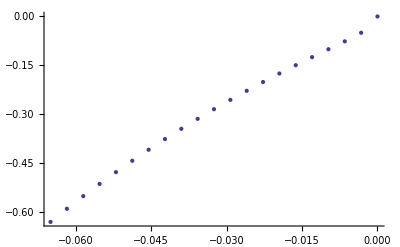

```mathematica
Vala[vec_]:=vec[[1]]/3-2vec[[2]]/Sqrt[3]
a=Table[{Vala[ListETotal[[i]]],Vala[Result[[i,3]]]},{i,1,Length[ListETotal]}]
ListPlot[a]
Clear[a]
```

```mathematica
Table[Vala[{ListETotal[[i,1]]K,ListETotal[[i,2]]2G}]/.exemple,{i,1,Length[ListETotal]}]
Table[Vala[{Result[[i,2,1]]K,Result[[i,2,2]]2G}]/.exemple,{i,1,Length[ListETotal]}]
```

{0.,-0.245556,-0.491111,-0.736667,-0.982222,-1.22778,-1.47333,-1.71889,-1.96444,-2.21,-2.45556,-2.70111,-2.94667,-3.19222,-3.43778,-3.68333,-3.92889,-4.17444,-4.42,-4.66556,-4.91111}

{0,-0.195418,-0.414537,-0.635839,-0.857105,-1.07785,-1.29793,-1.51726,-1.7358,-1.9535,-2.17033,-2.38622,-2.60114,-2.81504,-3.02787,-3.23958,-3.4501,-3.65939,-3.86739,-4.07404,-4.27929}

```mathematica
a=Derivatives[Result[[1,3]],Result[[2,3]]-Result[[1,3]],Result[[1,1]]];
{{a[[1,1]]Sqrt[3],a[[1,2]]},{a[[2,1]]Sqrt[3],a[[2,2]]},a[[3]]}
{ListETotal[[2]],Result[[2,2]],Result[[2,1]]}
```

lval = 0.133045

flval = 0.0532179

gradf2 = {-26.0371,0.}

derivT = {-0.00191967,0.0157458}

dlval = 17.0081

B lval = 0.08914

- C B E^(B lval) = -0.131844

dfval = -2.24242

one = 255.675

two = 84.2732

three = 0.

four = 0.

df2depsp = 339.949

epspponto = -0.00014703

trN2 = -45.0976

gammaponto = 3.26026×10^-6

deformPlast = {-0.0000848878,0.}

ST = {0,1}

deformElast = {-0.0000166248,0.000196822}

{{-0.000175825,0.000196822},{-0.00014703,0.},-0.00014703}

{{-0.000325,0.000187639},{-0.000275126,0.0000484644},-0.000275126}

```mathematica
ElastoPlastic[Result[[1,1]],Result[[1,2]],ListETotal[[2]]]
```

ETotal = {-0.000325,0.000187639}

SigI1xJ2 = {-0.0216667,0.0150111}

valf2 = 0.431788

subit {I1T→-0.0216667,J2T→0.0150111}

θ = -π

θ = -(19 π)/20

θ = -(9 π)/10

θ = -(17 π)/20

θ = -(4 π)/5

θ = -(3 π)/4

θ = -(7 π)/10

θ = -(13 π)/20

θ = -(3 π)/5

θ = -(11 π)/20

θ = -π/2

θ = -(9 π)/20

θ = -(2 π)/5

θ = -(7 π)/20

θ = -(3 π)/10

θ = -π/4

θ = -π/5

θ = -(3 π)/20

θ = -π/10

θ = -π/20

θ = 0

θ = π/20

θ = π/10

θ = (3 π)/20

θ = π/5

θ = π/4

θ = (3 π)/10

θ = (7 π)/20

θ = (2 π)/5

θ = (9 π)/20

θ = π/2

θ = (11 π)/20

θ = (3 π)/5

θ = (13 π)/20

θ = (7 π)/10

θ = (3 π)/4

θ = (4 π)/5

θ = (17 π)/20

θ = (9 π)/10

θ = (19 π)/20

θ = π

restheta = {5.67729,5.34003,5.12872,4.9867,4.87787,4.78283,4.69152,4.5989,4.5027,4.4021,4.29704,4.18782,4.07487,3.9587,3.83975,3.71847,3.59526,3.47045,3.34437,3.21729,3.08947,2.96115,3.45065,3.57936,3.70797,3.83632,3.96425,4.09163,4.21839,4.34455,4.47028,4.59604,4.72284,4.85265,4.98938,5.14073,5.32211,5.56417,5.91817,0.122311,0.605891}

θ = (19 π)/20

θ = (19 π)/20

residue = {0.122311,0.00034957}

tangent = {{3.32067,-242.53},{-0.000312192,1.33818}}

delu = {0.0568818,0.000274499}

θ = 2.92763

delepsp = -0.000274499

θ = 2.92763

residue = {-0.0229419,3.22682×10^-6}

tangent = {{4.02657,-202.504},{-0.000428652,1.33871}}

delu = {-0.00566767,5.95617×10^-7}

θ = 2.9333

delepsp = -0.000275094

θ = 2.9333

residue = {0.0000914666,3.16371×10^-8}

tangent = {{4.05591,-225.014},{-0.000417475,1.33881}}

delu = {0.0000242825,3.12026×10^-8}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {-1.41228×10^-9,5.93007×10^-13}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {-3.29334×10^-10,3.40229×10^-13}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,1.6263×10^-19}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {6.85528×10^-18,1.23612×10^-19}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,5.42101×10^-20}

Function2 = 2.22045×10^-16

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
{K,2G}/.exemple
{ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple
(%-Result[[2,3]])/.exemple
{%[[1]]/K,%[[2]]/(2G)}/.exemple
```

{66.6667,80}

{-0.216667,0.150111}

{-0.179007,0.117562}

{-0.0026851,0.00146953}

```mathematica
Result[[2]]
```

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
epsp=Result[[2,1]]
theta=2.5604883056356527;
l=LFunction[epsp];
fl=F[l]/.exemple;
i1theta=l+fl R Cos[theta]/.exemple;
i1=Result[[2,3,1]];
i1-i1theta;
sqj2=Result[[2,3,2]];
sqj2theta=fl Sin[theta];
sqj2theta-sqj2;
(l-i1)^2 /(fl R)^2 + sqj2^2/fl^2 -1/.exemple;
gfv1=2√3(i1-l)/(fl R)^2/.exemple;
√3 gfv1;
gfv2=√2 sqj2/fl^2;
sqj2/fl;
ep=Result[[2,2]];
ArcTan[ep[[1]],ep[[2]]]
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple
ArcTan[epprop[[1]],epprop[[2]]]
TmTt={K epprop[[1]],2G epprop[[2]]}/.exemple
sigtrial={ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple;
sigma=Result[[2,3]]
difsigma=(sigtrial-sigma)/.exemple;
ArcTan[difsigma[[1]],difsigma[[2]]]
ep-{difsigma[[1]]/K,difsigma[[2]]/(2G)}/.exemple
ArcTan[TmTt[[1]],TmTt[[2]]]
ArcTan[2 G R difsigma[[1]],3K difsigma[[2]]]/.exemple
theta
difsigma

Print[" delta gamma ",δγ2=epsp/epprop[[1]]]
Tepprop={K epprop[[1]],2G epprop[[2]]}/.exemple;
toto=Tepprop δγ2
ArcTan[difsigma[[1]],difsigma[[2]]]
ArcTan[toto[[1]],toto[[2]]]
δγ2 epprop-ep


Print["Checking stress functions"];
sigma
sqj2
l
fl
Print["gradf ",{epprop[[1]]/Sqrt[3],epprop[[2]]/Sqrt[2]}]
{sigma[[1]]/Sqrt[3],sigma[[2]]Sqrt[2]}

DLFunction[epsp]
B l/.exemple
dF[l]/.exemple
DLFunction[epsp]dF[l]/.exemple
a=DLFunction[epsp](2(l-i1))/(fl R)^2/.exemple
b=DLFunction[epsp](-(2(l-i1)^2)/(fl^3 R^2)dF[l])/.exemple
c=DLFunction[epsp](-(2sigma[[2]]^2)/fl^3 dF[l])/.exemple
Print["four ",DLFunction[epsp](-(2sigma[[2]]^2)/1 dF[l])/.exemple]
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,a=epponto=-gradFT/dfedep]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]

epsp=0;
i1=0;
sqj2=0;
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple;
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,b=epponto=-gradFT/dfedep]
Print["epponto medio ",(a+b)/2]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]


ClearAll[l,fl,i1,sqj2,gfv1,gfv2,epsp,theta,i1theta,sqj2theta,ep,epprop,TmTt,sigtrial,sigma,difsigma,Tepprop,toto,δγ2,dfedep,gradFT,epponto,a,b,c,gammaponto]
```

-0.000275126

2.96723

{-43.6165,7.68321}

2.96723

{-2907.77,614.657}

{-0.00332496,0.011134}

2.93327

{0.,0.}

2.93327

2.93327

2.56049

{-0.0183417,0.00387715}

delta gamma 6.30783×10^-6

{-0.0183417,0.00387715}

2.93327

2.93327

{5.42101×10^-20,-4.06576×10^-20}

Checking stress functions

{-0.00332496,0.011134}

0.011134

0.128354

0.0538354

gradf {-25.182,5.43285}

{-0.00191967,0.0157458}

17.0926

0.0859971

-0.13143

-2.24649

248.507

79.888

3.56967

four 0.000556972

331.965

0.133886

epponto -0.000403313

TrN2 -43.6165

gammaponto 9.2468×10^-6

316.564

0.0471204

epponto -0.00014885

epponto medio -0.000276081

TrN2 -42.5151

gammaponto 3.5011×10^-6

```mathematica
K
```

K